```mathematica
(* Code to visualize deconvolution fractions *)
(* Sevahn Vorperian, Quake Lab *)
```

```mathematica
fractions = Import["/Users/kayaneh/Documents/peeproject/code/deconvolve_urine/average_normal_supernatant_fractions_20230518.csv"]
```

{{,0},{Kidney epithelial cell,0.125965},{Prostate epithelia,0.100139},{Luminal cell of prostate epithelium,0.0779044},{Ionocyte/luminal epithelial cell of mammary gland,0.0710082},{Myeloid progenitor,0.0595641},{Intestinal tuft cell,0.0578658},{Basal cell,0.0453078},{Intestinal enterocyte,0.0415231},{Salivary/bronchial secretory cell,0.038838},{Schwann cell,0.034025},{Respiratory ciliated cell,0.0319499},{Intrahepatic cholangiocyte,0.0318023},{Pericyte cell,0.0262167},{Pulmonary ionocyte,0.0211155},{Neutrophil,0.017794},{Keratinocyte,0.0177056},{Respiratory secretory cell,0.0171808},{Thymocyte,0.0146042},{T cell,0.0142763},{Salivary gland cell,0.0139354},{B cell,0.0134897},{Mast cell,0.0130807},{Type ii pneumocyte,0.0113373},{Macrophage,0.0100459},{Mature conventional dendritic cell,0.00978452},{Plasmablast,0.00884472},{Platelet,0.00878333},{Pancreatic acinar cell,0.00859659},{Adventitial cell,0.00819065},{Cell of skeletal muscle,0.00720117},{Intestinal secretory cell,0.00672736},{Nk cell,0.00528857},{Hepatocyte,0.00479629},{Stromal cell,0.00478187},{Medullary thymic epithelial cell,0.00423099},{Pancreatic pp cell,0.00349351},{Endothelial cell,0.00312139},{Erythrocyte/erythroid progenitor,0.00226868},{Tendon cell,0.00205617},{Club cell/type i pneumocyte,0.00185798},{Smooth muscle cell,0.000799944},{Melanocyte,0.000754238},{Innate lymphoid cell,0.00071753},{Mesothelial cell,0.000455045},{Pancreatic alpha/beta cell,0.000218326},{Cardiac muscle cell,0.00019799},{Duodenum glandular cell,0.00015876}}

```mathematica
roundPower = 0.1;
percentThresh = 1.2; (* percentage cutoff for stacked bar chart vs main pie *)
scalePercents = 100; (* scale all percentages by 100 *)
superSmallThresh = 0.3; (* percentage cutoff for cell types with small fractional contirbutions *)
sampleCenter = "Normal Supernatant Average";
```

```mathematica
cellColorDict= <|"Kidney epithelial cell"->RGBColor[1., 0.8156862745098039, 0.],"Small"->RGBColor[1., 0.6666666666666666, 0.],"Keratinocyte"->RGBColor[0.9490196078431372, 0.3607843137254902, 0.32941176470588235],"Prostate epithelia"->RGBColor[0.8509803921568627, 0.011764705882352941, 0.40784313725490196],"Salivary gland cell"->RGBColor[0.8470588235294118, 0.11764705882352941, 0.3568627450980392],"Intestinal enterocyte"->RGBColor[0.6470588235294118, 0.2196078431372549, 0.3764705882352941],"Mature conventional dendritic cell"->RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],"Ionocyte/luminal epithelial cell of mammary gland"->RGBColor[0.047058823529411764, 0.3843137254901961, 0.5686274509803921],"Luminal cell of prostate epithelium"->RGBColor[0.1411764705882353, 0.4823529411764706, 0.6274509803921569],"Intestinal tuft cell"->RGBColor[0.5647058823529412, 0.8784313725490196, 0.9372549019607843],"Neutrophil"->RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],"B cell"->RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],"Intrahepatic cholangiocyte"->RGBColor[0.6274509803921569, 0.807843137254902, 0.8509803921568627],"Macrophage"->RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],"Bladder urothelial cell"->RGBColor[0., 0.4588235294117647, 0.6352941176470588],"Monocyte"->RGBColor[0.792156862745098, 0.9137254901960784, 1.],"Plasmablast"->RGBColor[0.24313725490196078, 0.5725490196078431, 0.8],"Stromal cell"->RGBColor[0.5137254901960784, 0.7725490196078432, 0.7450980392156863],"Respiratory ciliated cell"->RGBColor[0.00784313725490196, 0.5019607843137255, 0.5647058823529412],"Schwann cell"->RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],"Basal cell"->RGBColor[0.5607843137254902, 0.7529411764705882, 0.6627450980392157],"Pericyte cell"->RGBColor[0.12941176470588237, 0.5137254901960784, 0.5019607843137255],"Hepatocyte"->RGBColor[0.2823529411764706, 0.6235294117647059, 0.7098039215686275],"Salivary/bronchial secretory cell"->RGBColor[0.047058823529411764, 0.4823529411764706, 0.6196078431372549],"Very Small Contributors"->RGBColor[0., 0.5058823529411764, 0.6549019607843137],"Endothelial cell"->RGBColor[0.023529411764705882, 0.7450980392156863, 0.8823529411764706],"Thymocyte"->RGBColor[0., 0.6862745098039216, 0.7254901960784313],"Mesothelial cell"->RGBColor[0.3803921568627451, 0.6470588235294118, 0.7607843137254902],"Intestinal secretory cell"->RGBColor[0.08627450980392157, 0.5411764705882353, 0.6784313725490196],"Nk cell"->RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],"Myeloid progenitor"->RGBColor[0.8392156862745098, 0.1568627450980392, 0.1568627450980392],"Goblet cell"->RGBColor[0.9411764705882353, 0.44313725490196076, 0.403921568627451],"T cell"->RGBColor[0.9686274509803922, 0.4980392156862745, 0.],"Pulmonary ionocyte"->RGBColor[0.9882352941176471, 0.7490196078431373, 0.28627450980392155],"Adventitial cell"->RGBColor[0.9176470588235294, 0.8862745098039215, 0.7176470588235294],"Tendon cell"->RGBColor[0.7607843137254902, 0.9058823529411765, 0.8509803921568627],"Fibroblast/mesenchymal stem cell"->RGBColor[0.6627450980392157, 0.8392156862745098, 0.8980392156862745],"Basal cell of prostate epithelium"->RGBColor[0.49411764705882355, 0.7411764705882353, 0.7607843137254902],"Mast cell"->RGBColor[0.27450980392156865, 0.5607843137254902, 0.6862745098039216],"Erythrocyte/erythroid progenitor"->RGBColor[0.16470588235294117, 0.43529411764705883, 0.592156862745098],"Pancreatic ductal cell"->RGBColor[0.3568627450980392, 0.5215686274509804, 0.6666666666666666]|>
```

<|Kidney epithelial cell→RGBColor[1., 0.8156862745098039, 0.],Small→RGBColor[1., 0.6666666666666666, 0.],Keratinocyte→RGBColor[0.9490196078431372, 0.3607843137254902, 0.32941176470588235],Prostate epithelia→RGBColor[0.8509803921568627, 0.011764705882352941, 0.40784313725490196],Salivary gland cell→RGBColor[0.8470588235294118, 0.11764705882352941, 0.3568627450980392],Intestinal enterocyte→RGBColor[0.6470588235294118, 0.2196078431372549, 0.3764705882352941],Mature conventional dendritic cell→RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],Ionocyte/luminal epithelial cell of mammary gland→RGBColor[0.047058823529411764, 0.3843137254901961, 0.5686274509803921],Luminal cell of prostate epithelium→RGBColor[0.1411764705882353, 0.4823529411764706, 0.6274509803921569],Intestinal tuft cell→RGBColor[0.5647058823529412, 0.8784313725490196, 0.9372549019607843],Neutrophil→RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],B cell→RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],Intrahepatic cholangiocyte→RGBColor[0.6274509803921569, 0.807843137254902, 0.8509803921568627],Macrophage→RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],Bladder urothelial cell→RGBColor[0., 0.4588235294117647, 0.6352941176470588],Monocyte→RGBColor[0.792156862745098, 0.9137254901960784, 1.],Plasmablast→RGBColor[0.24313725490196078, 0.5725490196078431, 0.8],Stromal cell→RGBColor[0.5137254901960784, 0.7725490196078432, 0.7450980392156863],Respiratory ciliated cell→RGBColor[0.00784313725490196, 0.5019607843137255, 0.5647058823529412],Schwann cell→RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],Basal cell→RGBColor[0.5607843137254902, 0.7529411764705882, 0.6627450980392157],Pericyte cell→RGBColor[0.12941176470588237, 0.5137254901960784, 0.5019607843137255],Hepatocyte→RGBColor[0.2823529411764706, 0.6235294117647059, 0.7098039215686275],Salivary/bronchial secretory cell→RGBColor[0.047058823529411764, 0.4823529411764706, 0.6196078431372549],Very Small Contributors→RGBColor[0., 0.5058823529411764, 0.6549019607843137],Endothelial cell→RGBColor[0.023529411764705882, 0.7450980392156863, 0.8823529411764706],Thymocyte→RGBColor[0., 0.6862745098039216, 0.7254901960784313],Mesothelial cell→RGBColor[0.3803921568627451, 0.6470588235294118, 0.7607843137254902],Intestinal secretory cell→RGBColor[0.08627450980392157, 0.5411764705882353, 0.6784313725490196],Nk cell→RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],Myeloid progenitor→RGBColor[0.8392156862745098, 0.1568627450980392, 0.1568627450980392],Goblet cell→RGBColor[0.9411764705882353, 0.44313725490196076, 0.403921568627451],T cell→RGBColor[0.9686274509803922, 0.4980392156862745, 0.],Pulmonary ionocyte→RGBColor[0.9882352941176471, 0.7490196078431373, 0.28627450980392155],Adventitial cell→RGBColor[0.9176470588235294, 0.8862745098039215, 0.7176470588235294],Tendon cell→RGBColor[0.7607843137254902, 0.9058823529411765, 0.8509803921568627],Fibroblast/mesenchymal stem cell→RGBColor[0.6627450980392157, 0.8392156862745098, 0.8980392156862745],Basal cell of prostate epithelium→RGBColor[0.49411764705882355, 0.7411764705882353, 0.7607843137254902],Mast cell→RGBColor[0.27450980392156865, 0.5607843137254902, 0.6862745098039216],Erythrocyte/erythroid progenitor→RGBColor[0.16470588235294117, 0.43529411764705883, 0.592156862745098],Pancreatic ductal cell→RGBColor[0.3568627450980392, 0.5215686274509804, 0.6666666666666666]|>

```mathematica
fractions = fractions[[2;;]]; (* eliminate the center name *)
```

```mathematica
(* cellTypes = fractions[[1]][[2;;]] *)
cellTypes = fractions[[;;,1]]
```

{Kidney epithelial cell,Prostate epithelia,Luminal cell of prostate epithelium,Ionocyte/luminal epithelial cell of mammary gland,Myeloid progenitor,Intestinal tuft cell,Basal cell,Intestinal enterocyte,Salivary/bronchial secretory cell,Schwann cell,Respiratory ciliated cell,Intrahepatic cholangiocyte,Pericyte cell,Pulmonary ionocyte,Neutrophil,Keratinocyte,Respiratory secretory cell,Thymocyte,T cell,Salivary gland cell,B cell,Mast cell,Type ii pneumocyte,Macrophage,Mature conventional dendritic cell,Plasmablast,Platelet,Pancreatic acinar cell,Adventitial cell,Cell of skeletal muscle,Intestinal secretory cell,Nk cell,Hepatocyte,Stromal cell,Medullary thymic epithelial cell,Pancreatic pp cell,Endothelial cell,Erythrocyte/erythroid progenitor,Tendon cell,Club cell/type i pneumocyte,Smooth muscle cell,Melanocyte,Innate lymphoid cell,Mesothelial cell,Pancreatic alpha/beta cell,Cardiac muscle cell,Duodenum glandular cell}

```mathematica
(* fractions =fractions[[2;;,2;;]][[1]] *)
fractions = fractions[[;;,2]]
```

{0.125965,0.100139,0.0779044,0.0710082,0.0595641,0.0578658,0.0453078,0.0415231,0.038838,0.034025,0.0319499,0.0318023,0.0262167,0.0211155,0.017794,0.0177056,0.0171808,0.0146042,0.0142763,0.0139354,0.0134897,0.0130807,0.0113373,0.0100459,0.00978452,0.00884472,0.00878333,0.00859659,0.00819065,0.00720117,0.00672736,0.00528857,0.00479629,0.00478187,0.00423099,0.00349351,0.00312139,0.00226868,0.00205617,0.00185798,0.000799944,0.000754238,0.00071753,0.000455045,0.000218326,0.00019799,0.00015876}

```mathematica
Length[fractions]
```

47

```mathematica
Length[cellTypes]
```

47

```mathematica
(* fractions = Import["~/Documents/deconvolution/cellTypeFractions_10XDecon_07222020.xlsx"][[1]]; *)
```

```mathematica
contribs = fractions  (* excluded sample name and r, p-value, RMSE *)
```

{0.125965,0.100139,0.0779044,0.0710082,0.0595641,0.0578658,0.0453078,0.0415231,0.038838,0.034025,0.0319499,0.0318023,0.0262167,0.0211155,0.017794,0.0177056,0.0171808,0.0146042,0.0142763,0.0139354,0.0134897,0.0130807,0.0113373,0.0100459,0.00978452,0.00884472,0.00878333,0.00859659,0.00819065,0.00720117,0.00672736,0.00528857,0.00479629,0.00478187,0.00423099,0.00349351,0.00312139,0.00226868,0.00205617,0.00185798,0.000799944,0.000754238,0.00071753,0.000455045,0.000218326,0.00019799,0.00015876}

```mathematica
Length[fractions]
```

47

```mathematica
Length[cellTypes]
```

47

```mathematica
(* first get the zero index *)
```

```mathematica
zeroIndex = Position[contribs, val_/;val ≤ 0]
```

{}

```mathematica
(* drop it from the contributions and drop the corresponding labels *)
```

```mathematica
nonZeroVals = Delete[contribs, zeroIndex];
```

```mathematica
nonZeroVals = nonZeroVals * scalePercents
```

{12.5965,10.0139,7.79044,7.10082,5.95641,5.78658,4.53078,4.15231,3.8838,3.4025,3.19499,3.18023,2.62167,2.11155,1.7794,1.77056,1.71808,1.46042,1.42763,1.39354,1.34897,1.30807,1.13373,1.00459,0.978452,0.884472,0.878333,0.859659,0.819065,0.720117,0.672736,0.528857,0.479629,0.478187,0.423099,0.349351,0.312139,0.226868,0.205617,0.185798,0.0799944,0.0754238,0.071753,0.0455045,0.0218326,0.019799,0.015876}

```mathematica
Total[nonZeroVals]
```

100.

```mathematica
nonZeroCells = Delete[cellTypes, zeroIndex];
```

```mathematica
Length[nonZeroCells]
```

47

```mathematica
nonZeroCells
```

{Kidney epithelial cell,Prostate epithelia,Luminal cell of prostate epithelium,Ionocyte/luminal epithelial cell of mammary gland,Myeloid progenitor,Intestinal tuft cell,Basal cell,Intestinal enterocyte,Salivary/bronchial secretory cell,Schwann cell,Respiratory ciliated cell,Intrahepatic cholangiocyte,Pericyte cell,Pulmonary ionocyte,Neutrophil,Keratinocyte,Respiratory secretory cell,Thymocyte,T cell,Salivary gland cell,B cell,Mast cell,Type ii pneumocyte,Macrophage,Mature conventional dendritic cell,Plasmablast,Platelet,Pancreatic acinar cell,Adventitial cell,Cell of skeletal muscle,Intestinal secretory cell,Nk cell,Hepatocyte,Stromal cell,Medullary thymic epithelial cell,Pancreatic pp cell,Endothelial cell,Erythrocyte/erythroid progenitor,Tendon cell,Club cell/type i pneumocyte,Smooth muscle cell,Melanocyte,Innate lymphoid cell,Mesothelial cell,Pancreatic alpha/beta cell,Cardiac muscle cell,Duodenum glandular cell}

```mathematica
nonZeroVals
```

{12.5965,10.0139,7.79044,7.10082,5.95641,5.78658,4.53078,4.15231,3.8838,3.4025,3.19499,3.18023,2.62167,2.11155,1.7794,1.77056,1.71808,1.46042,1.42763,1.39354,1.34897,1.30807,1.13373,1.00459,0.978452,0.884472,0.878333,0.859659,0.819065,0.720117,0.672736,0.528857,0.479629,0.478187,0.423099,0.349351,0.312139,0.226868,0.205617,0.185798,0.0799944,0.0754238,0.071753,0.0455045,0.0218326,0.019799,0.015876}

```mathematica
(* nonZeroVals = nonZeroVals/Total[nonZeroVals] (* normalize to 1 *) did this normalization in python *)
```

```mathematica
nonZeroVals = Round[#, roundPower] &/@nonZeroVals (* round to 3 digits *)
```

{12.6,10.,7.8,7.1,6.,5.8,4.5,4.2,3.9,3.4,3.2,3.2,2.6,2.1,1.8,1.8,1.7,1.5,1.4,1.4,1.3,1.3,1.1,1.,1.,0.9,0.9,0.9,0.8,0.7,0.7,0.5,0.5,0.5,0.4,0.3,0.3,0.2,0.2,0.2,0.1,0.1,0.1,0.,0.,0.,0.}

```mathematica
Total[nonZeroVals]
```

100.

```mathematica
(* get index cell types that are less than one percent together for the bar chart *)
```

```mathematica
lt1Percent = Position[nonZeroVals, val_/;val  < percentThresh]
```

{{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47}}

```mathematica
(* now pull the cell types and their associated values and put in reverse order so it goes from smallest to largest *)
```

```mathematica
smallContribVals = Reverse[Part[nonZeroVals, # ]&/@ lt1Percent]
smallContribCells = Reverse[Part[nonZeroCells, #] &/@ lt1Percent];
```

{{0.},{0.},{0.},{0.},{0.1},{0.1},{0.1},{0.2},{0.2},{0.2},{0.3},{0.3},{0.4},{0.5},{0.5},{0.5},{0.7},{0.7},{0.8},{0.9},{0.9},{0.9},{1.},{1.},{1.1}}

```mathematica
(* get the indices where the elements are ≤ 0.1% or 0.001 *)
```

```mathematica
ltPt1Percent = Position[Flatten[smallContribVals], val_/;val  ≤ superSmallThresh]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12}}

```mathematica
(* get the sum of the values and the respective cell ≤ 0.1 % *)
fracsLTPt1 = Part[smallContribVals, # ] &/@ ltPt1Percent
cellsLTPt1 = Part[smallContribCells, #] &/@ ltPt1Percent
```

{{{0.}},{{0.}},{{0.}},{{0.}},{{0.1}},{{0.1}},{{0.1}},{{0.2}},{{0.2}},{{0.2}},{{0.3}},{{0.3}}}

{{{Duodenum glandular cell}},{{Cardiac muscle cell}},{{Pancreatic alpha/beta cell}},{{Mesothelial cell}},{{Innate lymphoid cell}},{{Melanocyte}},{{Smooth muscle cell}},{{Club cell/type i pneumocyte}},{{Tendon cell}},{{Erythrocyte/erythroid progenitor}},{{Endothelial cell}},{{Pancreatic pp cell}}}

```mathematica
totalSuperSmall = Total[Flatten[fracsLTPt1]]
```

1.5

```mathematica
(* now drop those small guys *)
```

```mathematica
goodSmallVals = Delete[smallContribVals, ltPt1Percent];
goodSmallCells = Delete[smallContribCells, ltPt1Percent];
```

```mathematica
goodSmallCells
```

{{Medullary thymic epithelial cell},{Stromal cell},{Hepatocyte},{Nk cell},{Intestinal secretory cell},{Cell of skeletal muscle},{Adventitial cell},{Pancreatic acinar cell},{Platelet},{Plasmablast},{Mature conventional dendritic cell},{Macrophage},{Type ii pneumocyte}}

```mathematica
(* add the sum of the remaining cells *)
goodSmallVals = AppendTo[goodSmallVals, {totalSuperSmall}]
goodSmallCells = AppendTo[goodSmallCells, {"Very Small Contributors"}]
```

{{0.4},{0.5},{0.5},{0.5},{0.7},{0.7},{0.8},{0.9},{0.9},{0.9},{1.},{1.},{1.1},{1.5}}

{{Medullary thymic epithelial cell},{Stromal cell},{Hepatocyte},{Nk cell},{Intestinal secretory cell},{Cell of skeletal muscle},{Adventitial cell},{Pancreatic acinar cell},{Platelet},{Plasmablast},{Mature conventional dendritic cell},{Macrophage},{Type ii pneumocyte},{Very Small Contributors}}

```mathematica
(* now sort this finalized "small cell" list *)
```

```mathematica
finalOrder = Reverse[Ordering[goodSmallVals]]
```

{14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
goodSmallVals = Flatten[Part[goodSmallVals , #] &/@ finalOrder]
```

{1.5,1.1,1.,1.,0.9,0.9,0.9,0.8,0.7,0.7,0.5,0.5,0.5,0.4}

```mathematica
goodSmallCells = Flatten[Part[goodSmallCells, #] &/@ finalOrder]
```

{Very Small Contributors,Type ii pneumocyte,Macrophage,Mature conventional dendritic cell,Plasmablast,Platelet,Pancreatic acinar cell,Adventitial cell,Cell of skeletal muscle,Intestinal secretory cell,Nk cell,Hepatocyte,Stromal cell,Medullary thymic epithelial cell}

```mathematica
(* now make the bar chart *)
```

```mathematica
shortlist =List[Flatten[Table[Callout[goodSmallVals[[#]], goodSmallCells[[#]],After,Appearance->"Leader",LeaderSize->{15,Automatic,2}],1] &/@Range[Length[goodSmallCells]]]];
```

```mathematica
shortlist
```

{{Callout[1.5,Very Small Contributors,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[1.1,Type ii pneumocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[1.,Macrophage,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[1.,Mature conventional dendritic cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.9,Plasmablast,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.9,Platelet,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.9,Pancreatic acinar cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.8,Adventitial cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,Cell of skeletal muscle,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,Intestinal secretory cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.5,Nk cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.5,Hepatocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.5,Stromal cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.4,Medullary thymic epithelial cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}]}}

```mathematica
piePal = Map [RGBColor,{"#0D3b66","#bee9e8","#62b6cb","#1b4965","#cae9ff","#5fa8d3","#f25c54","#EE964B","#f25c54", "#f26419", "#a4508b", "#f7567c","#7e1946", "#f6ae2d", "#68b0ab", "#5bba6f", "#9ece9a", "#c8d5b9","#b56576","#FFBF81","#FFD9CE"}]
```

{RGBColor[0.050980392156862744, 0.23137254901960785, 0.4],RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.10588235294117647, 0.28627450980392155, 0.396078431372549],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.9490196078431372, 0.3607843137254902, 0.32941176470588235],RGBColor[0.9333333333333333, 0.5882352941176471, 0.29411764705882354],RGBColor[0.9490196078431372, 0.3607843137254902, 0.32941176470588235],RGBColor[0.9490196078431372, 0.39215686274509803, 0.09803921568627451],RGBColor[0.6431372549019608, 0.3137254901960784, 0.5450980392156862],RGBColor[0.9686274509803922, 0.33725490196078434, 0.48627450980392156],RGBColor[0.49411764705882355, 0.09803921568627451, 0.27450980392156865],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.3568627450980392, 0.7294117647058823, 0.43529411764705883],RGBColor[0.6196078431372549, 0.807843137254902, 0.6039215686274509],RGBColor[0.7843137254901961, 0.8352941176470589, 0.7254901960784313],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[1., 0.7490196078431373, 0.5058823529411764],RGBColor[1., 0.8509803921568627, 0.807843137254902]}

```mathematica
Length[piePal]
```

21

```mathematica
(* would use LabelingSize function but its not available before version 11.3 
https://reference.wolfram.com/language/ref/LabelingSize.html*)
```

```mathematica
barPal = Map[RGBColor, {"#0081a7","#06BEE1","#00afb9","#61A5C2","#168AAD","#6d597a","#d62828","#f07167","#f77f00","#fcbf49","#eae2b7","#C2E7D9","#89b0ae",
 "#A9D6E5","#7EBDC2",
  "#468FAF", "#2A6F97", "#5B85AA",
  (* "#276FBF", *)"#457b9d","#6096ba",
"#414770", "#6D597A", "#b56576",(*"#E56B6F",*)"#FFBF81","#FFD9CE"}]
```

{RGBColor[0., 0.5058823529411764, 0.6549019607843137],RGBColor[0.023529411764705882, 0.7450980392156863, 0.8823529411764706],RGBColor[0., 0.6862745098039216, 0.7254901960784313],RGBColor[0.3803921568627451, 0.6470588235294118, 0.7607843137254902],RGBColor[0.08627450980392157, 0.5411764705882353, 0.6784313725490196],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.8392156862745098, 0.1568627450980392, 0.1568627450980392],RGBColor[0.9411764705882353, 0.44313725490196076, 0.403921568627451],RGBColor[0.9686274509803922, 0.4980392156862745, 0.],RGBColor[0.9882352941176471, 0.7490196078431373, 0.28627450980392155],RGBColor[0.9176470588235294, 0.8862745098039215, 0.7176470588235294],RGBColor[0.7607843137254902, 0.9058823529411765, 0.8509803921568627],RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706],RGBColor[0.6627450980392157, 0.8392156862745098, 0.8980392156862745],RGBColor[0.49411764705882355, 0.7411764705882353, 0.7607843137254902],RGBColor[0.27450980392156865, 0.5607843137254902, 0.6862745098039216],RGBColor[0.16470588235294117, 0.43529411764705883, 0.592156862745098],RGBColor[0.3568627450980392, 0.5215686274509804, 0.6666666666666666],RGBColor[0.27058823529411763, 0.4823529411764706, 0.615686274509804],RGBColor[0.3764705882352941, 0.5882352941176471, 0.7294117647058823],RGBColor[0.2549019607843137, 0.2784313725490196, 0.4392156862745098],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[1., 0.7490196078431373, 0.5058823529411764],RGBColor[1., 0.8509803921568627, 0.807843137254902]}

```mathematica
barPal = Lookup[cellColorDict, goodSmallCells]
```

{RGBColor[0., 0.5058823529411764, 0.6549019607843137],Missing[KeyAbsent,Type ii pneumocyte],RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.24313725490196078, 0.5725490196078431, 0.8],Missing[KeyAbsent,Platelet],Missing[KeyAbsent,Pancreatic acinar cell],RGBColor[0.9176470588235294, 0.8862745098039215, 0.7176470588235294],Missing[KeyAbsent,Cell of skeletal muscle],RGBColor[0.08627450980392157, 0.5411764705882353, 0.6784313725490196],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.2823529411764706, 0.6235294117647059, 0.7098039215686275],RGBColor[0.5137254901960784, 0.7725490196078432, 0.7450980392156863],Missing[KeyAbsent,Medullary thymic epithelial cell]}

BarChart::chsty: Value of option ChartStyle -> … is not a style or group of styles.

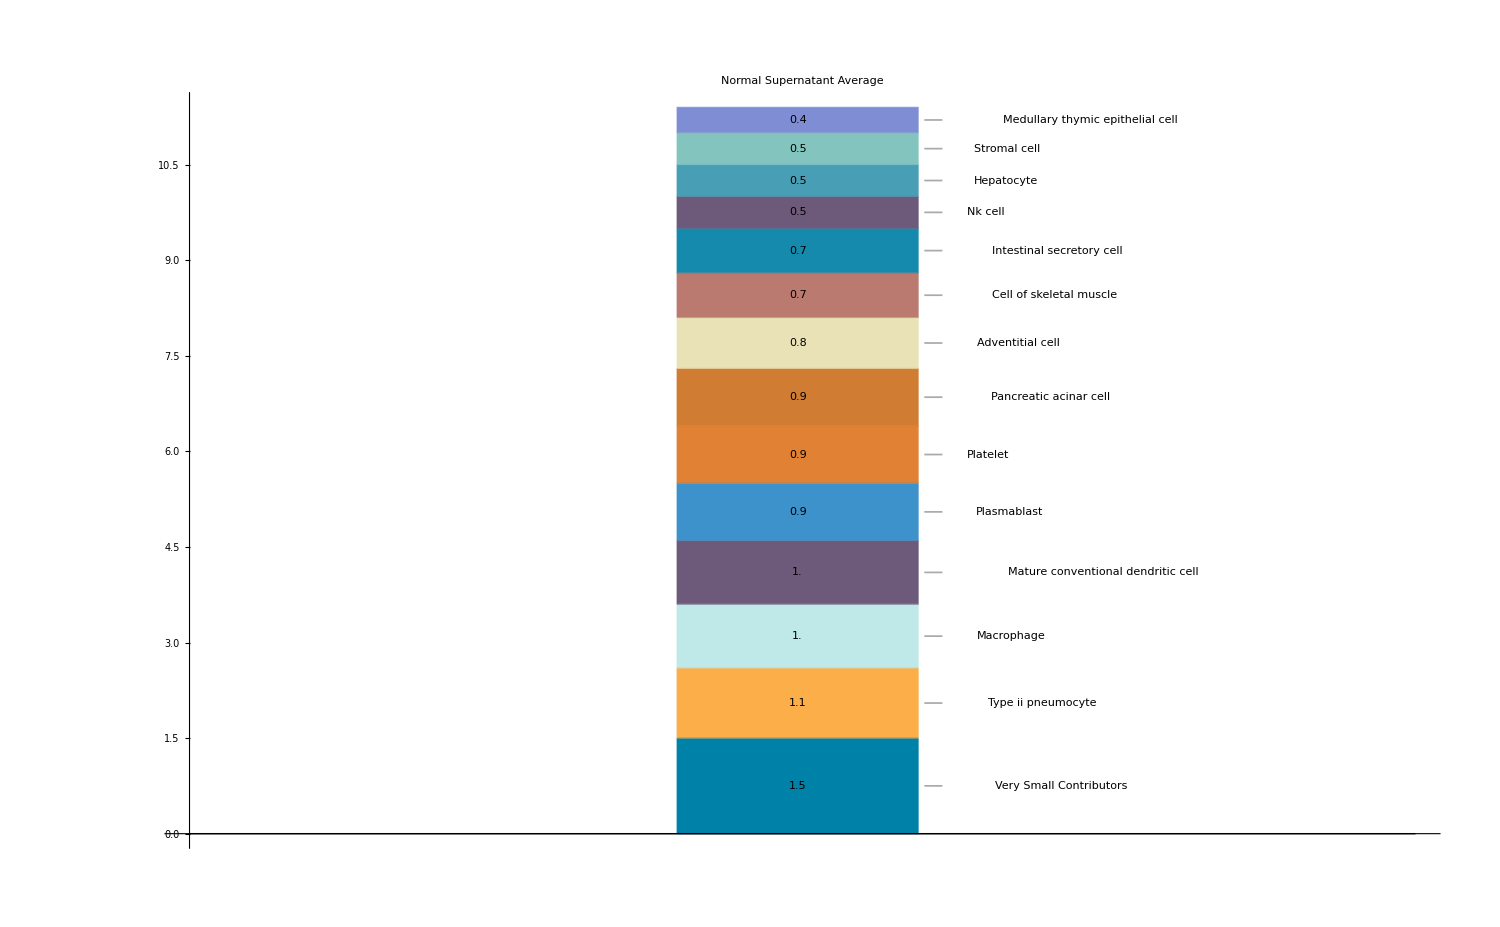

```mathematica
BarChart[shortlist,BarSpacing->2,ChartLayout->"Stacked",
ChartStyle-> barPal, ImageSize-> 1500, LabelingFunction ->( Placed[#1, Center]&), BaseStyle->{FontSize->20}, PlotLabel -> sampleCenter]
```

```mathematica
(* cool, now it's time to make the pie chart *)
```

```mathematica
gtPt1Percent = Position[Flatten[nonZeroVals], val_/;val  >=percentThresh ]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22}}

```mathematica
bigContribs = Part[nonZeroVals, #] &/@ gtPt1Percent
```

{{12.6},{10.},{7.8},{7.1},{6.},{5.8},{4.5},{4.2},{3.9},{3.4},{3.2},{3.2},{2.6},{2.1},{1.8},{1.8},{1.7},{1.5},{1.4},{1.4},{1.3},{1.3}}

```mathematica
bigCells = Part[nonZeroCells, #] &/@ gtPt1Percent
```

{{Kidney epithelial cell},{Prostate epithelia},{Luminal cell of prostate epithelium},{Ionocyte/luminal epithelial cell of mammary gland},{Myeloid progenitor},{Intestinal tuft cell},{Basal cell},{Intestinal enterocyte},{Salivary/bronchial secretory cell},{Schwann cell},{Respiratory ciliated cell},{Intrahepatic cholangiocyte},{Pericyte cell},{Pulmonary ionocyte},{Neutrophil},{Keratinocyte},{Respiratory secretory cell},{Thymocyte},{T cell},{Salivary gland cell},{B cell},{Mast cell}}

```mathematica
bigTot = Total[Flatten[bigContribs]] ;
smallContribTot = Total[Flatten[goodSmallVals]];
bigTot + smallContribTot (* cool, so we sum to 1 between small and big contributions *)
```

100.

```mathematica
(* add the sum of the small contributions *)
```

```mathematica
bigContribs= AppendTo[bigContribs, {smallContribTot}];
bigCells = AppendTo[bigCells, {"Small"}]
```

{{Kidney epithelial cell},{Prostate epithelia},{Luminal cell of prostate epithelium},{Ionocyte/luminal epithelial cell of mammary gland},{Myeloid progenitor},{Intestinal tuft cell},{Basal cell},{Intestinal enterocyte},{Salivary/bronchial secretory cell},{Schwann cell},{Respiratory ciliated cell},{Intrahepatic cholangiocyte},{Pericyte cell},{Pulmonary ionocyte},{Neutrophil},{Keratinocyte},{Respiratory secretory cell},{Thymocyte},{T cell},{Salivary gland cell},{B cell},{Mast cell},{Small}}

```mathematica
Total[Flatten[bigContribs]]
```

100.

```mathematica
(* now it's time to sort it from big to small *)
```

```mathematica
finalOrderBig = Reverse[Ordering[bigContribs]];
bigContribs = Flatten[Part[bigContribs, #] &/@ finalOrderBig];
bigCells = Flatten[Part[bigCells, #] &/@ finalOrderBig];
```

```mathematica
(* make the labels for the pie chart *)
```

```mathematica
bigContribs
```

{12.6,11.4,10.,7.8,7.1,6.,5.8,4.5,4.2,3.9,3.4,3.2,3.2,2.6,2.1,1.8,1.8,1.7,1.5,1.4,1.4,1.3,1.3}

```mathematica
test = Callout[bigContribs[[#]], bigCells[[#]],  Appearance -> "Leader"]&/@ Range[Length[bigCells]]
```

{Callout[12.6,Kidney epithelial cell,Appearance→Leader],Callout[11.4,Small,Appearance→Leader],Callout[10.,Prostate epithelia,Appearance→Leader],Callout[7.8,Luminal cell of prostate epithelium,Appearance→Leader],Callout[7.1,Ionocyte/luminal epithelial cell of mammary gland,Appearance→Leader],Callout[6.,Myeloid progenitor,Appearance→Leader],Callout[5.8,Intestinal tuft cell,Appearance→Leader],Callout[4.5,Basal cell,Appearance→Leader],Callout[4.2,Intestinal enterocyte,Appearance→Leader],Callout[3.9,Salivary/bronchial secretory cell,Appearance→Leader],Callout[3.4,Schwann cell,Appearance→Leader],Callout[3.2,Intrahepatic cholangiocyte,Appearance→Leader],Callout[3.2,Respiratory ciliated cell,Appearance→Leader],Callout[2.6,Pericyte cell,Appearance→Leader],Callout[2.1,Pulmonary ionocyte,Appearance→Leader],Callout[1.8,Keratinocyte,Appearance→Leader],Callout[1.8,Neutrophil,Appearance→Leader],Callout[1.7,Respiratory secretory cell,Appearance→Leader],Callout[1.5,Thymocyte,Appearance→Leader],Callout[1.4,Salivary gland cell,Appearance→Leader],Callout[1.4,T cell,Appearance→Leader],Callout[1.3,Mast cell,Appearance→Leader],Callout[1.3,B cell,Appearance→Leader]}

```mathematica
"#84a98c"
```

#84a98c

```mathematica
piePal = Map [RGBColor,{"#bee9e8" ,"#62b6cb","#1b4965","#cae9ff","#5fa8d3",  "#a4508b", "#BC412B","#f26419","#f8c7cc", "#f7567c","#7e1946", "#f6ae2d", "#68b0ab","#84a98c", "#5bba6f", "#9ece9a", "#c8d5b9", "#355070","#6d597a","#b56576","#e56b6f","#eaac8b","#89b0ae",  "#457b9d","#555b6e","#6096ba","#014f86"}]
```

{RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.10588235294117647, 0.28627450980392155, 0.396078431372549],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.6431372549019608, 0.3137254901960784, 0.5450980392156862],RGBColor[0.7372549019607844, 0.2549019607843137, 0.16862745098039217],RGBColor[0.9490196078431372, 0.39215686274509803, 0.09803921568627451],RGBColor[0.9725490196078431, 0.7803921568627451, 0.8],RGBColor[0.9686274509803922, 0.33725490196078434, 0.48627450980392156],RGBColor[0.49411764705882355, 0.09803921568627451, 0.27450980392156865],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.5176470588235295, 0.6627450980392157, 0.5490196078431373],RGBColor[0.3568627450980392, 0.7294117647058823, 0.43529411764705883],RGBColor[0.6196078431372549, 0.807843137254902, 0.6039215686274509],RGBColor[0.7843137254901961, 0.8352941176470589, 0.7254901960784313],RGBColor[0.20784313725490197, 0.3137254901960784, 0.4392156862745098],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[0.8980392156862745, 0.4196078431372549, 0.43529411764705883],RGBColor[0.9176470588235294, 0.6745098039215687, 0.5450980392156862],RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706],RGBColor[0.27058823529411763, 0.4823529411764706, 0.615686274509804],RGBColor[0.3333333333333333, 0.3568627450980392, 0.43137254901960786],RGBColor[0.3764705882352941, 0.5882352941176471, 0.7294117647058823],RGBColor[0.00392156862745098, 0.30980392156862746, 0.5254901960784314]}

```mathematica
"#0d3b66",
```

```mathematica
piePal =Map[RGBColor, {
"#ffc857",
"#ff7f51",
"#f25c54",
"#83C5BE",
"#028090","#68B0AB",
"#8FC0A9","#5fa8d3","#62b6cb",
"#bee9e8" ,
"#0075a2","#cae9ff","#3e92cc",
"#d90368",
"#ff637d",
"#f88dad","#a53860",

"#d90429", "#ff5a5f","#f4f1bb", "#f2c49b"}]
```

{RGBColor[1., 0.7843137254901961, 0.3411764705882353],RGBColor[1., 0.4980392156862745, 0.3176470588235294],RGBColor[0.9490196078431372, 0.3607843137254902, 0.32941176470588235],RGBColor[0.5137254901960784, 0.7725490196078432, 0.7450980392156863],RGBColor[0.00784313725490196, 0.5019607843137255, 0.5647058823529412],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.5607843137254902, 0.7529411764705882, 0.6627450980392157],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0., 0.4588235294117647, 0.6352941176470588],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.24313725490196078, 0.5725490196078431, 0.8],RGBColor[0.8509803921568627, 0.011764705882352941, 0.40784313725490196],RGBColor[1., 0.38823529411764707, 0.49019607843137253],RGBColor[0.9725490196078431, 0.5529411764705883, 0.6784313725490196],RGBColor[0.6470588235294118, 0.2196078431372549, 0.3764705882352941],RGBColor[0.8509803921568627, 0.01568627450980392, 0.1607843137254902],RGBColor[1., 0.35294117647058826, 0.37254901960784315],RGBColor[0.9568627450980393, 0.9450980392156862, 0.7333333333333333],RGBColor[0.9490196078431372, 0.7686274509803922, 0.6078431372549019]}

```mathematica
piePal = Lookup[cellColorDict, #] &/@bigCells
```

{RGBColor[1., 0.8156862745098039, 0.],RGBColor[1., 0.6666666666666666, 0.],RGBColor[0.8509803921568627, 0.011764705882352941, 0.40784313725490196],RGBColor[0.1411764705882353, 0.4823529411764706, 0.6274509803921569],RGBColor[0.047058823529411764, 0.3843137254901961, 0.5686274509803921],RGBColor[0.8392156862745098, 0.1568627450980392, 0.1568627450980392],RGBColor[0.5647058823529412, 0.8784313725490196, 0.9372549019607843],RGBColor[0.5607843137254902, 0.7529411764705882, 0.6627450980392157],RGBColor[0.6470588235294118, 0.2196078431372549, 0.3764705882352941],RGBColor[0.047058823529411764, 0.4823529411764706, 0.6196078431372549],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.6274509803921569, 0.807843137254902, 0.8509803921568627],RGBColor[0.00784313725490196, 0.5019607843137255, 0.5647058823529412],RGBColor[0.12941176470588237, 0.5137254901960784, 0.5019607843137255],RGBColor[0.9882352941176471, 0.7490196078431373, 0.28627450980392155],RGBColor[0.9490196078431372, 0.3607843137254902, 0.32941176470588235],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],Missing[KeyAbsent,Respiratory secretory cell],RGBColor[0., 0.6862745098039216, 0.7254901960784313],RGBColor[0.8470588235294118, 0.11764705882352941, 0.3568627450980392],RGBColor[0.9686274509803922, 0.4980392156862745, 0.],RGBColor[0.27450980392156865, 0.5607843137254902, 0.6862745098039216],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549]}

Lookup::invrl: The argument cellColorDict is not a valid Association or a list of rules.

Lookup::invrl: The argument cellColorDict is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

{Lookup[cellColorDict,Small],Lookup[cellColorDict,kidney epithelial cell],Lookup[cellColorDict,club cell of prostate epithelium/hillock cell of prostate epithelium/hillock-club cell of prostate epithelium],Lookup[cellColorDict,luminal cell of prostate epithelium],Lookup[cellColorDict,ionocyte/luminal epithelial cell of mammary gland],Lookup[cellColorDict,myeloid progenitor],Lookup[cellColorDict,intestinal tuft cell],Lookup[cellColorDict,basal cell],Lookup[cellColorDict,enterocyte of epithelium of large intestine/enterocyte of epithelium of small intestine/intestinal crypt stem cell of large intestine/large intestine goblet cell/mature enterocyte/paneth cell of epithelium of large intestine/small intestine goblet cell],Lookup[cellColorDict,duct epithelial cell/serous cell of epithelium of bronchus],Lookup[cellColorDict,schwann cell],Lookup[cellColorDict,intrahepatic cholangiocyte],Lookup[cellColorDict,ciliated cell/lung ciliated cell],Lookup[cellColorDict,pericyte cell],Lookup[cellColorDict,pulmonary ionocyte],Lookup[cellColorDict,keratinocyte],Lookup[cellColorDict,neutrophil],Lookup[cellColorDict,respiratory goblet cell/respiratory mucous cell/serous cell of epithelium of trachea],Lookup[cellColorDict,thymocyte]}

```mathematica
PieChart[test, ChartStyle->piePal, SectorOrigin->{ -Pi / 3,1},BaseStyle->{FontSize->20},  ImageSize-> 1500,ImagePadding->{{240,60},{0,0}},LabelingFunction ->"RadialCenter", PlotLabel->sampleCenter]
```

PieChart::chsty: Value of option ChartStyle -> … is not a style or group of styles.

-Graphics-

```mathematica
(* could try adding percents to the fractions but i wont *)
```

```mathematica
stringPercents = TextString[bigContribs[[#]]]<>"%" &/@ Range[Length[bigContribs]]
```

{12.6%,11.4%,10.0%,7.8%,7.1%,6.0%,5.8%,4.5%,4.2%,3.9%,3.4%,3.2%,3.2%,2.6%,2.1%,1.8%,1.8%,1.7%,1.5%,1.4%,1.4%,1.3%,1.3%}